# Image processing

## Sample image (100 bar)

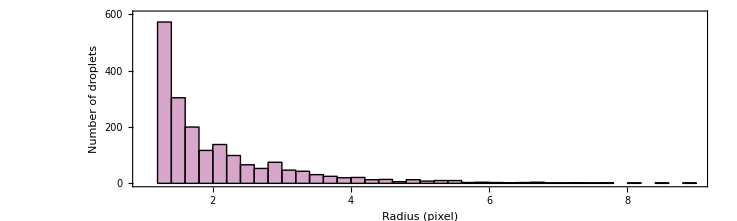
-Graphics- | -Graphics-
-Graphics- |

```mathematica
(* -- import -- *)
sourceFile=NotebookDirectory[]<>"data/imgSample.mx";
raw=Import[sourceFile];

(* -- image adjust -- *)
imgSelect=ImageAdjust[raw];

(* -- detection function -- *)
detectDroplets[img_Image]:=Block[{centers,radii,intensities},
{centers,radii,intensities}=ComponentMeasurements[img,{"Centroid","EquivalentDiskRadius","TotalIntensity"},#AdjacentBorderCount==0&&5<#Area<300&,CornerNeighbors->False][[All,2]]ᵀ;
Return[{centers,radii,intensities}];
];

(* -- counting -- *)
{centers,radii,intensities}=detectDroplets[imgSelect];

(* -- annotation 1: elapsed time -- *)
t=Graphics[{
Text[
Style["Time: 0 min.",FontSize->14,FontColor->White],
{20,600-20},{-1,1}]
}];

(* -- annotation 2: scale -- *)
sc=Graphics[{
{AbsoluteThickness[2],White,Line[{{600-20,600-20},{600-210-20,600-20}}]},
Text[
Style["1 mm",FontSize->14,FontColor->White],
{600-20,600-20},{1,1}]
}];

(* -- annotation 3: pressure -- *)
p=Graphics[{
Text[
Style["p = 100 bar",FontSize->14,FontColor->White],
{20,20},{-1,-1}]
}];

(* -- annotation 4: counter -- *)
org=Graphics[{
Text[
Style["Original Image",FontSize->14,FontColor->White],
{600-20,20},{1,-1}]
}];
ct=Graphics[{
Text[
Style["Detected #: "<>ToString@Length[centers],FontSize->14,FontColor->White],
{600-20,20},{1,-1}]
}];

(* -- images -- *)
circlesCoord=Partition[Riffle[centers,radii],2];
imgDetect=HighlightImage[
ImageAdjust@imgSelect,Graphics[{
EdgeForm[{RGBColor[.7,.3,.6,1],AbsoluteThickness[1]}],
FaceForm[Transparent],
Disk@@@circlesCoord}],
ImageSize->(65*2)*(72/25.4)];

imgAnnot=Show[{imgDetect,sc,t,p,ct},ImageSize->(65*2)*(72/25.4)];

(* -- histogram -- *)
hist=Histogram[

radii,{.2},

PlotRange->{{1,9},{0,600}},
PlotRangePadding->0,
PlotRangeClipping->False,

LabelStyle->{FontSize->14,FontWeight->Plain},

ChartStyle->Directive[FaceForm[RGBColor[.7,.3,.6,.5]],EdgeForm[{Black,Opacity[1],AbsoluteThickness[1]}]],

Frame->True,
FrameTicks->{Table[{{i,i,{.015,0}},{i,Null,{.015,0}}},{i,0,600,200}]ᵀ,Table[{{i,i,{.015,0}},{i,Null,{.015,0}}},{i,0,10,1}]ᵀ},
FrameLabel->{{"Number of droplets",None},{"Radius (pixel)",None}},
FrameStyle->Directive[Black,Opacity[1],AbsoluteThickness[1]],

GridLines->None,
ImagePadding->{{50,5},{45,10}},
AspectRatio->.3,
ImageSize->(130*2)*(72/25.4)

];

(* -- merge plots -- *)
gf=Grid[{
{Show[{imgSelect,t,sc,p,org},ImageSize->(65*2)*(72/25.4)],
Show[{imgDetect,ct},ImageSize->(65*2)*(72/25.4)]},
{hist,SpanFromLeft}
},
Spacings->0];
Print[gf];
Export[NotebookDirectory[]<>"imgProcess.pdf",gf];
```

# Number density

## By pressure

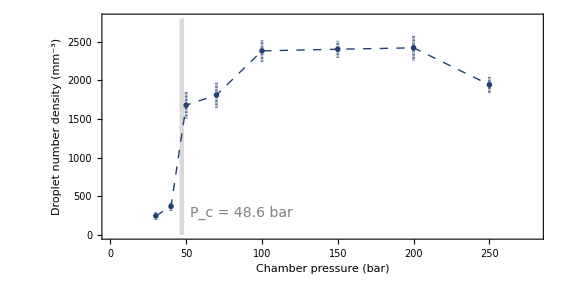

```mathematica
(* -- import data -- *)
numDens=Import[NotebookDirectory[]<>"data/raising/numDens.mx"];

(* -- plot -- *)
gfa=ListLinePlot[

numDens,

Prolog->{{FaceForm[{LightGray,Opacity[1]}],EdgeForm[Transparent],Rectangle[{48.630-3,0},{48.630,2800}]}},

Epilog->{
Text[Style["a",{FontColor->Black,FontSize->18,FontWeight->Bold}],ImageScaled[{0,1}],{-1,1}],
Text[Style[StringForm["`1` = 48.6 bar",Subscript[Style["P",Italic],"c"]],{FontColor->Gray,FontSize->14,FontWeight->Plain}],Scaled@{.2,.15},{-1,1}]
},

Joined->True,
ScalingFunctions->"Linear",

PlotRange->{{0,280},{0,2800}},
PlotRangePadding->0,
PlotRangeClipping->False,

LabelStyle->{FontSize->14,FontWeight->Plain},

PlotStyle->{RGBColor[.14,.25,.44,1],Opacity[1],AbsoluteThickness[1],AbsoluteDashing[6]},

PlotMarkers->Graphics[{EdgeForm[{RGBColor[.14,.25,.44,1],AbsoluteThickness[2]}],FaceForm[{RGBColor[.54,.62,.72,1]}],Disk[{0,0},Offset[4]]}],

IntervalMarkers->"Bars",
IntervalMarkersStyle->{RGBColor[.14,.25,.44,1],Opacity[1],AbsoluteThickness[2],AbsoluteDashing[0]},

Frame->True,
FrameTicks->{
{Table[{i,i,{.015,0}},{i,0,3000,500}],
Table[{i,Null,{.015,0}},{i,0,3000,500}]},
{Table[{i,If[Mod[i,50]==0,i,Null],{If[Mod[i,50]==0,.015,.008],0}},{i,0,300,25}],
Table[{i,Null,{If[Mod[i,50]==0,.015,.008],0}},{i,0,300,25}]}
},
FrameLabel->{{"Droplet number density (mm^-3)",None},{"Chamber pressure (bar)",None}},
FrameStyle->Directive[Black,Opacity[1],AbsoluteThickness[1]],

GridLines->None,
ImagePadding->{{60,15},{45,20}},
ImageSize->(100*2)*(72/25.4),
AspectRatio->0.5

];

Print[gfa];
```

## Compression rate

```mathematica
(* -- import data -- *)
raw=Import[NotebookDirectory[]<>"data/raising/compressor.mx"];
dt=raw;

(* -- fit -- *)
Clear[t];
lm=LinearModelFit[dt,t,t];
lb=SetPrecision[Normal[lm],3];
rate=lm["BestFitParameters"][[2]];
fdt=Table[{t,lm[t]},{t,0,10.6,.1}];

(* -- plot -- *)
gfb=ListLinePlot[

{
dt[[2;;;;3]],
Callout[fdt,
Style["P(t) = "<>ToString[lb],
{FontColor->Darker@Gray,FontSize->14,FontWeight->Plain}],
Automatic,4.1,
LeaderSize->{{25,-75 °,3},{12,0 °}},
CalloutStyle->{{Darker@Gray,Opacity[1],AbsoluteThickness[1]}},
CalloutMarker->Arrowheads[.025],
Frame->False,FrameMargins->3,Background->Transparent]
},

Epilog->{
Text[Style["b",{FontColor->Black,FontSize->18,FontWeight->Bold}],ImageScaled[{0,1}],{-1,1}]
},

Joined->{False,True},
ScalingFunctions->"Linear",

PlotRange->{{0,10.6},{0,230}},
PlotRangePadding->0,
PlotRangeClipping->False,

LabelStyle->{FontSize->14,FontWeight->Plain},

PlotStyle->{
None,
{Darker@Gray,Opacity[1],AbsoluteThickness[1],AbsoluteDashing[4]}
},

PlotMarkers->{
Graphics[{EdgeForm[{Black,AbsoluteThickness[1]}],FaceForm[{RGBColor[.53,.73,.53,1]}],Disk[{0,0},Offset[4]]}],
None
},

PlotLegends->Placed[
LineLegend[
{None,{Darker@Gray,Opacity[1],AbsoluteThickness[1],AbsoluteDashing[4]}},
{"Data","Fit"},
LabelStyle->{FontColor->Black,FontSize->14,FontWeight->Plain},
LegendMarkers->{
Graphics[{EdgeForm[{Black,Opacity[1],AbsoluteThickness[1]}],FaceForm[{RGBColor[.53,.73,.53,1]}],Disk[{0,0},Offset[3]]}],
None
},
LegendMarkerSize->{30,10},
LegendMargins->1,LegendLayout->"Column"],
{Scaled@{.05,.85},{0,1}}],

Frame->True,
FrameTicks->{
{Table[{i,If[Mod[i,100]==0,i,Null],{If[Mod[i,100]==0,.015,.008],0}},{i,0,220,20}],
Table[{i,Null,{If[Mod[i,100]==0,.015,.008],0}},{i,0,220,20}]},
{Table[{i,If[Mod[i,2]==0,i,Null],{If[Mod[i,2]==0,.015,.008],0}},{i,0,10,1}],
Table[{i,Null,{If[Mod[i,2]==0,.015,.008],0}},{i,0,10,1}]}
},
FrameLabel->{{"Pressure (bar)",None},{"Compressing time (min.)",None}},
FrameStyle->Directive[Black,Opacity[1],AbsoluteThickness[1]],

GridLines->None,
ImagePadding->{{60,15},{45,20}},
ImageSize->(100*2)*(72/25.4),
AspectRatio->0.3

];

Print[gfb];
```

-Graphics-

## Merge figures

```mathematica
gf=Grid[{{gfa},{gfb}},Spacings->0];
Print[gf];
Export[NotebookDirectory[]<>"numdens.pdf",gf];
```

-Graphics-

# Evaporation time

## By time

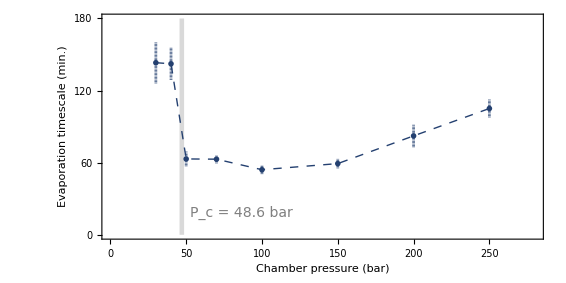

```mathematica
(* -- import data -- *)
lifetime=Import[NotebookDirectory[]<>"data/lifetime/lifetime.mx"];

(* -- plot -- *)
gfa=ListLinePlot[

lifetime,

Prolog->{{FaceForm[{LightGray,Opacity[1]}],EdgeForm[Transparent],Rectangle[{48.630-3,0},{48.630,180}]}},

Epilog->{
Text[Style["a",{FontColor->Black,FontSize->18,FontWeight->Bold}],ImageScaled[{0,1}],{-1,1}],
Text[Style[StringForm["`1` = 48.6 bar",Subscript[Style["P",Italic],"c"]],{FontColor->Gray,FontSize->14,FontWeight->Plain}],Scaled@{.2,.15},{-1,1}]
},

Joined->True,
ScalingFunctions->"Linear",

PlotRange->{{0,280},{0,180}},
PlotRangePadding->0,
PlotRangeClipping->False,

LabelStyle->{FontSize->14,FontWeight->Plain},

PlotStyle->{RGBColor[.14,.25,.44,1],Opacity[1],AbsoluteThickness[1],AbsoluteDashing[6]},

PlotMarkers->Graphics[{EdgeForm[{RGBColor[.14,.25,.44,1],AbsoluteThickness[2]}],FaceForm[{RGBColor[.54,.62,.72]}],Disk[{0,0},Offset[4]]}],

IntervalMarkers->"Bars",
IntervalMarkersStyle->{RGBColor[.14,.25,.44,1],Opacity[1],AbsoluteThickness[2],AbsoluteDashing[0]},

Frame->True,
FrameTicks->{
{Table[{i,If[Mod[i,60]==0,i,Null],{If[Mod[i,60]==0,.015,.008],0}},{i,0,180,20}],
Table[{i,Null,{If[Mod[i,60]==0,.015,.008],0}},{i,0,180,20}]},
{Table[{i,If[Mod[i,50]==0,i,Null],{If[Mod[i,50]==0,.015,.008],0}},{i,0,300,25}],
Table[{i,Null,{If[Mod[i,50]==0,.015,.008],0}},{i,0,300,25}]}
},
FrameLabel->{{"Evaporation timescale (min.)",None},{"Chamber pressure (bar)",None}},
FrameStyle->Directive[Black,Opacity[1],AbsoluteThickness[1]],

GridLines->None,
ImagePadding->{{60,15},{45,20}},
ImageSize->(100*2)*(72/25.4),
AspectRatio->0.5

];

Print[gfa];
```

## Selected pressures

```mathematica
(* -- import data -- *)
raw=Table[Import[NotebookDirectory[]<>ToString@StringForm["data/lifetime/`1`.mx",i]],{i,{100,250}}];

(* -- fit -- *)
expFit[dt_]:=Block[{nlm,fdt,τ},
Clear[a,b,t];
nlm=NonlinearModelFit[dt,a Exp[-t/b],{{a,1000},{b,30}},t];
fdt=Table[{t,nlm[t]},{t,0,120,.1}];
τ=SetPrecision[b Log[10]/.nlm["BestFitParameters"],3];
Return[{fdt,τ}];
];

{fdt1,τ1}=expFit[raw[[1]]];
{fdt2,τ2}=expFit[raw[[2]]];

(* -- plot -- *)
gfb=ListLinePlot[

{
raw[[1,2;;;;6]],
raw[[2,2;;;;6]],
Callout[fdt1,
Style[ToString[τ1]<>" (min.)",
{FontColor->Darker@Gray,FontSize->14,FontWeight->Plain}],
Automatic,57,
LeaderSize->{{20,-135 °,0},{10,180 °}},
CalloutStyle->{{Darker@Gray,Opacity[1],AbsoluteThickness[1]}},
CalloutMarker->Arrowheads[.025],
Frame->False,FrameMargins->3,Background->Transparent],
Callout[fdt2,
Style[ToString[τ2]<>" (min.)",
{FontColor->Darker@Gray,FontSize->14,FontWeight->Plain}],
Automatic,65,
LeaderSize->{{25,60°,0},{15,0 °}},
CalloutStyle->{{Darker@Gray,Opacity[1],AbsoluteThickness[1]}},
CalloutMarker->Arrowheads[.025],
Frame->False,FrameMargins->3,Background->Transparent]
},

Epilog->{
Text[Style["b",{FontColor->Black,FontSize->18,FontWeight->Bold}],ImageScaled[{0,1}],{-1,1}]
},

Joined->{False,False,True,True},
ScalingFunctions->"Log",

PlotRange->{{0,120},{10,3000}},
PlotRangePadding->0,
PlotRangeClipping->False,

LabelStyle->{FontSize->14,FontWeight->Plain},

PlotStyle->{
None,
None,
Directive[Darker@Gray,Opacity[1],AbsoluteThickness[1],AbsoluteDashing[8]],
Directive[Darker@Gray,Opacity[1],AbsoluteThickness[1],AbsoluteDashing[8]]
},

PlotMarkers->{
{Graphics[{
EdgeForm[{Black,Opacity[1],AbsoluteThickness[1]}],
FaceForm[{Lighter@Purple,Opacity[1]}],
RegularPolygon[3]},PlotRangePadding->0],Offset[9]},
{Graphics[{
EdgeForm[{Black,Opacity[1],AbsoluteThickness[1]}],
FaceForm[{Pink,Opacity[1]}],
RegularPolygon[4]},PlotRangePadding->0],Offset[9]},
None,
None
},

PlotLegends->Placed[
LineLegend[
{None,None,Directive[Darker@Gray,Opacity[1],AbsoluteThickness[1],AbsoluteDashing[8]]},
{"100 bar","250 bar","Fit"},
LabelStyle->{FontColor->Black,FontSize->14,FontWeight->Plain},
LegendMarkers->{
Graphics[{
EdgeForm[{Black,Opacity[1],AbsoluteThickness[1]}],
FaceForm[{Lighter@Purple,Opacity[1]}],
RegularPolygon[3]},PlotRangePadding->0],
Graphics[{
EdgeForm[{Black,Opacity[1],AbsoluteThickness[1]}],
FaceForm[{Pink,Opacity[1]}],
RegularPolygon[4]},PlotRangePadding->0],
Graphics[]
},
LegendMarkerSize->{{30,10}},
LegendMargins->1,LegendLayout->"Row"],
{Scaled@{.02,.06},{0,0}}],

Frame->True,
FrameTicks->{
{Table[{i,If[IntegerQ@Log10@i,Superscript[10,Log10@i],Null],{If[IntegerQ@Log10@i,.015,.008],0}},{i,#idx}],
Table[{i,Null,{If[IntegerQ@Log10@i,.015,.008],0}},{i,#idx}]}&
[<|"idx"->Part[Union@Flatten@Outer[Times,Range[0,10,1],PowerRange[1,10000,10]],2;;]|>],
{Table[{i,If[Mod[i,30]==0,i,Null],{If[Mod[i,30]==0,.015,.008],0}},{i,0,120,10}],
Table[{i,Null,{If[Mod[i,30]==0,.015,.008],0}},{i,0,120,10}]}
},
FrameLabel->{{"Density (mm^-3)",None},{"Time (min.)",None}},
FrameLabel->MapThread[StringJoin[Table["  ",#],#2]&,{{5,1},{"x","y"}}],
FrameStyle->Directive[Black,Opacity[1],AbsoluteThickness[1]],

GridLines->None,
ImagePadding->{{60,15},{45,20}},
ImageSize->(100*2)*(72/25.4),
AspectRatio->0.3

];

Print[gfb];
```

-Graphics-

## Merge figures

```mathematica
gf=Grid[{{gfa},{gfb}},Spacings->0];
Print[gf];
Export[NotebookDirectory[]<>"evaporation.pdf",gf];
```

-Graphics-